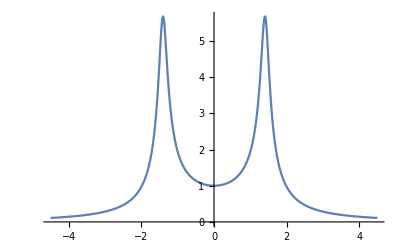

```mathematica
Plot[(64/(64-63 w^2+16 w^4))^.5, {w,-4.5,4.5}]
```

```mathematica
f[w_]:=(64/(64-63 w^2+16 w^4))^.5
```

```mathematica
f'[w]
```

-4. (-126 w+64 w^3) (1/(64-63 w^2+16 w^4))^1.5

```mathematica
Solve[{f'[w]==0,f''[w]<0},w]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{w→-1.40312},{w→1.40312}}

```mathematica
f[1.40312]
```

5.67908